# Ibraheem Al-Yousef PHYS422 HW.2 04/02/2023

## Problem 4):

### a):

```mathematica
ρ1[r_]:=1/(1+Exp[(r-R)/a])
```

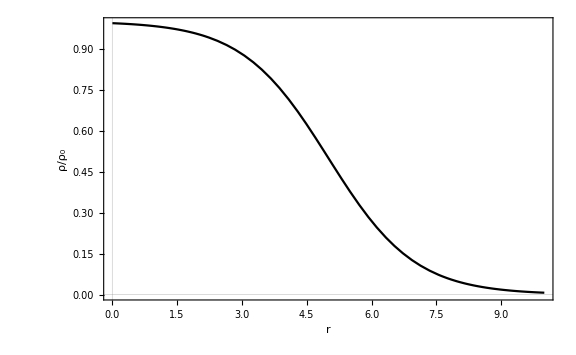

```mathematica
Plot[ρ1[r]/.a->1/.R->5,{r,0,10},PlotStyle->Black,PlotTheme->"Scientific",FrameLabel->{"r","ρ/ρ_0"},ImageSize->Large,LabelStyle->{16,GrayLevel[0]}]
```

### b):

### c):

### d):

From a manual :

```mathematica
Assuming[a>0,Integrate[r^2/(1+Exp[(r-R)/a]),{r,0,∞}]/Integrate[1/(1+Exp[(r-R)/a]),{r,0,∞}]]//FullSimplify//TraditionalForm
```

-(2 a^2 3-ⅇ^(R/a))/(log(ⅇ^(R/a)+1))

## Problem 6):

### a):

Using Bohr’s model, and a friend’s help :

### b):

Using Eq. 3.13 :

```mathematica
2/5*(26^4*9*10^9*(1.6*10^-19)*(R)^2)/a^3/.a->5.29177210903*10^-11/.R->1.3*10^-15 * 55.847^1/3
```

1.04029

## Problem 7):

### a):

```mathematica
BE[Z_,A_,M_]:=(Z*Subscript[m, p]+(A-Z)Subscript[m, n]-M)cc/.cc->931.5/.Subscript[m, p]->1.007825/.Subscript[m, n]->1.008665
```

```mathematica
BE[8,15,15.0030654]
```

111.957

```mathematica
BE[8,15,15.000109]
```

114.71

```mathematica
BE[7,15,15.000109]-BE[8,15,15.0030654]
```

3.53635

### b):

```mathematica
ColoumbEnergy[Z_]:=-3/5*9*10^9*1/R(Z^2*(1.6*10^-19))
```

```mathematica
Reduce[(BE[7,15,15.000109]-BE[8,15,15.0030654])*10^6==ColoumbEnergy[7]-ColoumbEnergy[8],R]
```

R==3.6648×10^-15